# Investigating Ecological Energy and Population Dynamics in Artificial Colonies Through Creation of an Agent-Based Modeling System with Detailed Interactively-Seeded Environmental Parameters

## Yash Juneja, Om Kalyani, and Shreraj Sainani - WELP 2025-26

## Abstract

In this work, we present a custom bioenergetics-informed ecological Agent-Based Modeling (ABM) toolbox for colonies of artificial organisms in the Wolfram Language and an investigation of energy and population dynamics with connections to real-world biology using this toolbox. Unlike previous Agent-Based Modeling projects done in the Wolfram Language, this interactive toolbox provides the user with the ability to change and visualize the effects of many more parameters on the outcomes of artificial colonies such as resolution of simulation time-discretization, sensing and interaction abilities of organisms, metabolic rates, lifespans, exploration/foraging behaviors, reproductive frequencies, and bioenergetics like digestion and reproduction energies. In the investigations performed using this toolbox, we show that ecological models produced by the toolbox mimic population dynamics on a macro-level seen in real-world ecology through experimentation on metabolic rates, primary production rates, caloric densities and reproductive frequencies with a logistic analysis of population growth and collection of other demographic data.

## Introduction

The processes by which life interacts with its environment, sustains itself, and reproduces are complex and intricately shaped by environmental factors and evolution. Agent-Based Modeling (ABM) simulations, while greatly simplified, can provide interesting theory that can provide a basis and a framework for actual studies of ecological behaviors and traits in organisms. Agent-Based Modeling simulations consist of agents representing organisms that interact with each other and their environment through simple rules. As the simulation evolves through time, the rules produce interesting behavior among the agents that can be studied. These rules ideally mimic real life to create a realistic, albeit simplified, simulation. Our model works as a toolbox for producing ecological simulations of colonies of artificial organisms and experimenting with how changing organisms’ characteristics or their environment, including, but not limited to, factors like metabolism, energy, reproduction age, and food availability, can influence population dynamics such as population growth, carrying capacity, age distributions, and life expectancies. The toolbox’s simulation logic incorporates movement, organisms dynamically sensing their environment and adjusting foraging and mating decisions, energy consumption, reproduction, and aging, as well as a visualization that maps each timestep to show how agents undergo all of these behaviors, which are informed through bioenergetics. Bioenergetics is the study of how organisms acquire, transform, store, and expend energy, and how those energy flows determine biological outcomes like growth, reproduction, movement, and survival. 

	With this toolbox, we create several experiments and graphs that show dynamics like logistic population growth and carrying capacity, the distribution of first reproduction ages, and life expectancies are affected by environmental parameters. Since our model has constrained space that introduces competition between agents (if two agents attempt to eat the same food it is determined randomly which eats it) and a constrained amount of food that is spawned (simulating primary production in an ecosystem), the environment naturally has a limited potential for growth, and the populations of our colonies naturally lend themselves towards logistic growth. Logistic growth is governed by the following differential equation, which embeds the constrained nature of the population growth into its structure:

dP/dt= rP(1-P/K)		(1)

P here is the population size as a function of t, the time. r is called the intrinsic growth rate and and K is the carrying capacity. When the population is very small, the (1-P/K) is close to 1 as P << K. Thus the population grows exponentially according to r, hence its name. Once the P approaches K, that term becomes significantly smaller than 1 and begins to dampen how fast the population grows, exemplifying how a population’s growth slows down as it approaches the maximum amount its environment can hold due to competition for resources leading to reduced overall prosperity of the population. In biology, there is usually a fluctuation around the carrying capacity as time goes on, as a population increases over the carrying capacity and ends up correcting due to the inability of the environment to support that excess population, but the asymptotic behavior of a logistic curve follows the average of those fluctuations in the long run, and thus describes the carrying capacity of a population. Separating and integrating this differential equation gives the form that we use among other curves to fit to our data for analysis:

P(t)= K/(1 + Ae^(-r t))		(2)

This equation provides information about the initial population through an analysis of A, carrying capacity K, and unconstrained growth rate r in a useful form.

	Overall, through these experiments, we show how simple rules can influence a population’s dynamics and characteristics, and how our Agent-Based Modeling toolbox can be used as a flexible foundation for studying further ecological systems and emergent population-level and agent-level behaviors.

## High-Level Model Development

### [this is where we will include lit review and research to back up our model choices. I’m thinking that this will be similar to the implementation section of our project proposal and maybe include a little bit of our project plan as well.]

### Current Scope [<-- Replace this with a few sections giving a high-level description of how our model works, so that the following sections have a framing and don’t seem arbitrary.]

From paper: If there is sufficient energy intake, an animal allocates the energy obtained in the order: maintenance, growth, reproduction, energy storage, until its energy stores reach an optimal level. If there is a shortfall, the priorities for maintenance and growth/reproduction remain the same until reserves fall to a critical threshold below which all are allocated to maintenance. [cite]

## Legend

something bolded - it’s an important word/symbol

CodeText - used to briefly explain smaller specific bits of code.

functionName[] - Text formatted like this references a specific function

parameter - Text formatted like this references a model or agent parameter (see Model Parameters and createAgent[])

## Model Parameters

These are model parameters stored as an association that set the rules for a simulation, and a user may freely tweak them to model certain environmental scenarios or use these as independent variables to run empirical experiments. Most functions of the model take in this parameters association to understand how they should work and to what extent their functions should affect model/agent state. Comments following each parameter outlines its purpose. Parameters, and thus the model, is defined in nondimensionalized arbitrary units: arbitrary distance units denoted (D), arbitrary time units denoted (T), and arbitrary energy units denoted (E) throughout.

```mathematica
parameters = <|
  "proximityRadius" -> 0.5, (*How close two things (agent/food, agent/agent) need to be to interact (eat, reproduce, etc.)*)
  "sensingDistance" -> 4, (*How far away agents can sense in D units, and by consequence intentionally travel to, pieces of food or other agents like mating partners*)
  "metabolism" -> 0.05, (*How much energy in E untis is expended each timestep by an agent*)
  "dt" -> 0.1, (*The timestep in arbitrary T units used in the time-discretization of the simulation*)
  "foodEnergy" -> 5.0, (*How much energy is gained from one piece of food for an agent*)
  "foodSpawnCooldown" -> 1, (*The cooldown in T of food spawning*)
  "nFoodSpawn" -> 5, (*The number of pieces of food spawned at random locations every time foodSpawnCooldown passes*)
  "nStartingAgents" -> 4, (*The number of agents the simulation starts with*)
  "nStartingFood" -> 4, (*The number of pieces of food that the simulation starts with*)
  "squareBounds" -> {0, 20}, (*The bounds of the model in D, with both dimensions of the model taking this range of numbers--
  the lower bound must be 0, and by consequence of this design, the model environment is square.*)
  "startingEnergy" -> 10, (*The amount of energy in E that an agent starts with*)
  "stepLength" -> 0.4, (*How far an agent can travel in one timestep in D, if they choose to travel*)
  "dirChangeProb" -> 0.025, (*If an agent is not intentionally moving towards food or a mate, 
  and exploring instead, this is the probability at any timestep that they will change their exploration direction. This controls their foraging and mating behaviors.*)
  "lifespan" -> 30, (*How long in T an agent is allowed to live*)
  "maxEnergy" -> 10, (*The most energy an agent can store in E*)
  "imageSize" -> 500, (*How large, in pixels, the size of the simulation is*)
  "agentSize" -> 0.01, (*The radius of an agent blob in the visualization in D, not pixels*)
  "foodSize" -> 0.0075, (*The radius of a piece of food in the visualization in D, not pixels*)
  "reproductionRadius" -> 1.0, (*How close in D two agents must be to reproduce with each other*)
  "minReproductionEnergy" -> 5.0, (*The minimum energy required for an agent to reproduce. Must be > than reproductionEnergyCost below*)
  "minReproductionAge" -> 4.0, (*Reproductive maturity age in T for an agent*)
  "reproductionEnergyCost" -> 2.0, (*The energy cost to reproduce to an agent*)
  "reproductionCooldown" -> 2, (*How long in T an agent must wait before reproducing again after reproducing. Constrains reproductive output*)
  "epsilon" -> 0.001, (*Smoothing parameter used to avoid numerical divergences. How small a distance bewteen two agents can theoretically get with the toolbox*)
  "rnd" -> N@10^(-3) (*The rounding used for the toolbox*)
|>;
```

To reference a parameter, use the string name of the parameter as the key for the global parameters association. This is how parameters are accessed within our code.

```mathematica
parameters["dt"]
```

0.1

## Core Model

### Data Structures

Before the rest of the toolbox was built, the core aspects of the model like agents that moved and consumed food were built first. The food in a model at any time is represented by a list of positions of pieces of food. Forthe data structure of the model as a whole, see Model Initialization.

createAgent[]is used to initialize agent associations. The data structure for agents was chosen to be an association so that specific attributes of agents that describe their state can be accessed through keys. Each agent attribute is commented with a description of its nature

```mathematica
createAgent[pos_, energy_, age_, id_, currentDirection_, parents_:{-1, -1}, reproductionCooldown_] := <|
    "pos" -> pos, (*The current position of an agent in the environment, length 2 array*)
    "energy" -> energy, (*The current energy of an agent*)
    "age" -> age, (*The current age of an agent*)
	"id" -> id, (*A unique identifer given to each agent created throughout the history of the simulation instance*)
	"currentDirection" -> currentDirection, (*The current direction the agent is exploring in or seeking food/mates in; value from [0, 2pi)*)
	"parents" -> parents, (*The ids of the agent's parents in a length 2 array. If the agent is one of the primordial starting agents, {-1, -1} is given to this value.
	used to determine familial relations for the purpose of incest prevention--a parent will naturally not reproduce with their child throughout almost all species*)
    "reproductionCooldown" -> reproductionCooldown
|>
```

### Core Functions

These functions are the basic operations needed for core model functionality.

For any interactions to occur, an object must be within another’s proximityRadius.  This goes for an agent and a piece of food, an agent and another agent for reproduction.

```mathematica
checkWithinRadius[p1_, p2_, r_] := EuclideanDistance[p1, p2] <= r;
```

EuclidianDistance[] is used in the checkWithinRadius[] function to verify the interaction condition of proximityRadius throughout simulation.

A function called findNearestSensableFoodInfo[] is used to find the nearest sensable (within sensingDistance) food to an agent so agents can seek and eat food. It returns this nearest sensable food’s distance, index in the food list, and position.

```mathematica
findNearestSensableFoodInfo[agent_, foodPositions_List, params_] := Module[
    {agentPos, foodPosAndI, foodsWithinRadiusPosAndI, dists},
    agentPos = agent["pos"];
    foodPosAndI = Table[{foodPositions[[i]], i}, {i, Length[foodPositions]}];
    foodsWithinRadiusPosAndI = Select[foodPosAndI, checkWithinRadius[agentPos, #[[1]], params["sensingDistance"]]&];
    If[
        Length[foodsWithinRadiusPosAndI] == 0,
        {-1, -1, -1}, (*no food*)
        dists = {EuclideanDistance[agentPos, #[[1]]], #[[2]], #[[1]]}& /@ foodsWithinRadiusPosAndI;
        First@MinimalBy[dists, First]
    ]
]
```

The function first compiles the food positions and indexes, and then isolates the ones that are within sensing distance of the agent. If no pieces of food make it into that isolation, then there are none within sensing distance and {-1, -1, -!} is returned. Else, the closest food’s {distance, index in the food list, position in the environment} is returned.

spawnFoods[]takes in a food list and adds new foods with the amount corresponding to the nFoodSpawn parameter. Rounding is used to prevent excess precision which increases the memory needed to save a simulation to a file (17.988838327 takes up more space then 17.989 in a .csv file).

```mathematica
spawnFoods[foods_, params_] := Join[foods, Round[RandomReal[params["squareBounds"], {params["nFoodSpawn"], 2}], params["rnd"]]]
```

To spawn food at the appropriate time, spawnFoodCheck[] updates the model’s food list with a spawnFoods[]operation when appropriate according to the foodSpawnCooldown parameter.

```mathematica
spawnFoodCheck[model_, params_] := Module[
    {model2 = model},
	model2["foods"] = If[
        Mod[model["time"], params["foodSpawnCooldown"]] < 10^(-1),
        spawnFoods[model["foods"], params],
        model["foods"]
    ];
	model2
]
```

< 10^(-1) is used instead of == 0 to not have to worry about integer vs. float mismatch issues. 0 should work in theory but did not. This solution is sloppy and is bad programming practice; it should be considered a temporary band-aid.

randomizeAndKill[] is a simulation management function that kills agents if they’ve reached any death conditions and randomizes their order by virtue of shuffling the agent list so that no agents are consistently prioritized over others during iteration in case two or more agents are near the same piece of food or both trying to reproduce with the same agent--the operation will be done on whichever comes first, but it is truly random so long as the order gets randomized during every timestep.

```mathematica
randomizeAndKill[model_, params_] := Module[
    {agents = model["agents"], model2=model},	
	agents = RandomSample[agents];
	model2["agents"] = Select[agents, (#["age"] < params["lifespan"] && #["energy"] > 0)&];
	model2
]
```

metabolizeAgents[]applies the metabolism operation to all agents for a timestep.

```mathematica
metabolizeAgents[model_, params_] := Module[
    {agents = model["agents"], model2=model},
	agents = MapAt[(# - params["metabolism"])&, agents, {All, "energy"}];
	model2["agents"] = agents;
	model2
]
```

ageAgents[]ages agents by one timestep dt during a timestep.

```mathematica
ageAgents[model_, params_] := Module[
    {agents = model["agents"], model2=model},
	agents = MapAt[(# + params["dt"])&, agents, {All, "age"}];
	model2["agents"] = agents;
	model2
]
```

explorationOrIntentionalWalk[] is the function that makes an agent walk in the current direction it’s moving in. This current direction depends on the sensory input it receives from its environment, and this is determined in the agentActions[]function in Agent Rules and Behavior.

```mathematica
explorationOrIntentionalWalk[agent_, params_] := Module[ (*direction is set in agentActions[], depending on exploration or intentional*)
	{agent2 = agent, currentDir = agent["currentDirection"], newPos, min, max},
	{min, max} = params["squareBounds"];
	newPos = agent2["pos"] + {params["stepLength"] * currentDir[[1]], params["stepLength"] * currentDir[[2]]};
	agent2["pos"] = Clip[newPos, {min, max}];
	agent2
]
```

agentEat[]is used to update agents’ energy when they eat a piece of food according to the foodEnergy parameter. The specific food that is being eaten is removed concurrently when this function is called from the model’s food list in [agent actions...].

```mathematica
agentEat[agent_, params_] := Module[
    {agent2 = agent, newE},
	newE = agent2["energy"] + params["foodEnergy"];
	agent2["energy"] = If[newE > params["maxEnergy"], params["maxEnergy"], newE];
	agent2
]
```

Through the If[]statement in the function, agentEat[] ensures that the energy does not exceed the maxEnergy

## Agent Rules and Behavior

Excluding reproduction [at the moment, (we need to use the paper to see if we should have reproduction in here or outside)], the main agent decision logic for a timestep occurs in the function agentActions. Agents will consume food if they are within the required proximityRadius to eat it, and otherwise they will move following their movement rules:  [if there is a sensable food or instead another agent I can reproduce with (if I have enough energy), move towards it, prioritizing reproduction if possible. Else, explore in a random direction according to direction agent attribute currentDirection I’m currently exploring in. If I’m exploring in a random direction, I have a 0.2 chance this timestep that I’m going to switch directions]

```mathematica
agentActions[model_, params_] :=  Module[
    {model2 = model, agents = model["agents"], foods = model["foods"], agent, nearFoodI, nearFoodDist},
	agents = Table[
		agent = agents[[i]];
		{nearFoodDist, nearFoodI} = findNearestSensableFoodPosAndI[agent, foods, params];
		If[
            nearFoodI>=1 && nearFoodDist < params["proximityRadius"], 
			foods = Delete[foods, nearFoodI]; agentEat[agent, params], 
			randomActionWalk[agent, params]
        ],
	    {i, Length@agents}
    ];
	model2["foods"] = foods;
	model2["agents"] = agents;
	model2
]
```

## Reproduction

Introducing reproduction is crucial to simulate real animal behaviors. When two agents meet, they produce an offspring that inherits a  position between them and a fresh slice of energy. Our functionality has four main parts working together: a way to give every agent an identity, rules for deciding who is allowed to mate with whom, and the reproduction step itself.

Every agent has a unique integer id, assigned when the agent is created. Every agent also has the ids of both their parents. The founding agents, the first agents in the simulation, have no parents and are simply marked with {-1, -1}. These are all part of the agent association:

```mathematica
createAgent[pos_,energy_,age_,id_,currentDirection_,parents_:{-1,-1},reproductionCooldown_]:=<|
"pos"->pos,
"energy"->energy,
"age"->age,"id"->id,
"currentDirection"->currentDirection,(*unit vector*)
"parents"->parents,
 "reproductionCooldown"->reproductionCooldown
 |>
```

The nextAgentId is created in inizializeModel to one more than the founding population, so the first agent created is given the next unused id: 
"nextAgentID" -> nStartingAgents + 1

areRelated[ai, aj] returns True if two agents share a close family tie, and is used to prevent incestuous pairings. It checks three conditions joined by Or: whether aj’s id appears in ai’s parent list (aj is a parent of ai), whether ai is a parent of aj, or whether the two agents have the identical set of parents (making them siblings). The sibling check sorts both parent lists before comparing so that parent order does not matter, and it explicitly excludes the founding agents, whose parents are {-1, -1}, so that the original population is not treated as one large sibling group.

```mathematica
areRelated[ai_, aj_] := Or[
    MemberQ[ai["parents"], aj["id"]],   
    MemberQ[aj["parents"], ai["id"]], 
    (ai["parents"] =!= {-1, -1} && Sort[ai["parents"]] === Sort[aj["parents"]])
]
```

reproduceAgents[model, params] carries out the actual reproduction step for a timestep. It iterates over every agent and finds its closest candidate partner, then re-checks the full mating predicate inline (the same distance, energy, age, cooldown, and relatedness conditions). When a pair qualifies and neither partner has already reproduced this timestep, both parents pay reproductionEnergyCost and have their cooldown reset, and a new agent is created at the midpoint between the parents with half of startingEnergy, age 0, the next unused id, a random heading, and both parents’ ids recorded. The new id counter advances, both partners are flagged as having reproduced so each mates at most once per step, and at the end the newborns are appended to the population and nextAgentID is saved back into the model. (Note: this cell looks up the partner with findClosestAgentI, but the function defined in the notebook is findClosestMateI; the two names need to be reconciled.)

```mathematica
reproduceAgents[model_, params_] := Module[
    {
        agents = model["agents"], model2 = model, newAgents = {},
        reproduced, nextID, j, ai, aj, dist, midPos, newAgent, newDir
    },

  nextID = model["nextAgentID"];
  reproduced = ConstantArray[False, Length[agents]];

  Do[
    If[reproduced[[i]], Continue[]];
    j = findClosestAgentI[i, agents];
    If[j == -1 || reproduced[[j]], Continue[]];

    ai = agents[[i]];
    aj = agents[[j]];
    dist = EuclideanDistance[ai["pos"], aj["pos"]];

    If[dist <= params["reproductionRadius"] &&
       ai["energy"] >= params["minReproductionEnergy"] &&
       aj["energy"] >= params["minReproductionEnergy"] &&
       ai["age"] >= params["minReproductionAge"] &&
       aj["age"] >= params["minReproductionAge"] &&
        ai["reproductionCooldown"] <= 0 &&
        aj["reproductionCooldown"] <= 0 &&
       !areRelated[ai, aj],

      (* both parents pay energy cost *)
      agents[[i]] = <|ai,
      "energy" -> ai["energy"] - params["reproductionEnergyCost"],
      "reproductionCooldown" -> params["reproductionCooldown"]|>;
      agents[[j]] = <|aj,
      "energy" -> aj["energy"] - params["reproductionEnergyCost"],
      "reproductionCooldown" -> params["reproductionCooldown"]|>;

      midPos = (ai["pos"] + aj["pos"]) / 2;
      newDir = {Cos[#], Sin[#]} &[RandomReal[{0, 2 Pi}]];
      newAgent = createAgent[midPos, params["startingEnergy"]/2, 0.0, nextID, newDir, {ai["id"], aj["id"]}, params["reproductionCooldown"]];
      AppendTo[newAgents, newAgent];
      nextID++;

      reproduced[[i]] = True;
      reproduced[[j]] = True;

    ];
  , {i, Length[agents]}];

  model2["agents"] = Join[agents, newAgents];
  model2["nextAgentID"] = nextID;
  model2
]
```

A reproduction cooldown is needed because, without one, any qualifying pair would reproduce on every single timestep they remained close and energetic, producing unrealistic runaway population growth. The cooldown imposes a refractory period: after reproducing, an agent’s reproductionCooldown is set to a positive value and it cannot mate again until that value returns to 0. decrementReproductionCooldowns[model, params] is what counts it down - each timestep it reduces every agent’s reproductionCooldown by dt, using Max[# - dt, 0] so the value never drops below zero, at which point the agent becomes eligible to reproduce again.

```mathematica
decrementReproductionCooldowns[model_, params_] := Module[
    {agents = model["agents"], model2 = model},
	agents = MapAt[Max[# - params["dt"], 0]&, agents, {All, "reproductionCooldown"}];
	model2["agents"] = agents;
	model2
]
```

## Model Initialization

The initializeModel[] function returns an initialized model initialized according to the model parameters. It is set equal to a global variable to represent the model when doing operations on the model at the top level, like running the simulation.

```mathematica
initializeModel[params_] :=

  Module[{agents, foods, nStartingAgents, nStartingFood, startingEnergy, min, max},  

    nStartingAgents = params["nStartingAgents"]; (*parameter for number of agents*)
    nStartingFood = params["nStartingFood"]; (*parameter for number of food items*)
    startingEnergy = params["startingEnergy"];
    {min, max} = params["squareBounds"];

    agents =
    Table[
      createAgent[RandomReal[{min, max}, 2], startingEnergy, 0.0, i, RandomReal[{0, 2 Pi}]], {i, nStartingAgents}
    ];

    foods = RandomReal[{min, max}, {nStartingFood, 2}];
	
    <| 
      "agents" -> agents, (*list of agent associations*)
      "foods" -> foods, (*list of food coordinates*)
      "bounds" -> {min, max},
      "time" -> 0,
      "nextAgentID" -> nStartingAgents + 1
    |>
 ]
```

The association returned is the model with the association data structure as defined earlier in Core Model → Data Structures.

## Model Propagation

The propagateModelStep[] function propagates the model by one timestep, doing the operations that occur during a timestep sequentially: spawning food if it’s the appropriate time,  removing agents that are dead and randomizing, doing the main agent action decision logic, [doing the separate reproduction actions (should not be separate?)], metabolizing the agents, aging the agents, and advancing time in the simulation.

```mathematica
propagateModelStep[params_, model_] := Module[{model2=model, params2=params},
  params2["nextAgentID"] = model2["nextAgentID"]; (*huh?*)
  model2 = spawnFoodCheck[model2, params];
  model2 = randomizeAndKill[model2, params]; (*randomization*)
  model2 = agentActions[model2, params];
  model2 = reproduceAgents[model2, params2]; (*why do we have params2?*)
  model2 = metabolizeAgents[model2, params];
  model2 = ageAgents[model2, params];
  model2["time"] = model2["time"] + params["dt"];
  model2
];
```

genSimulationStates is used to generate the entire simulation, which becomes a list of model states, with each index in the list being being a model object representing the state of the simulation after an amount of time steps that is that index.

```mathematica
genSimulationStates[params_, model_, timesteps_] := Module[{model2 = model}, Join[{model},Table[model2 = propagateModelStep[params, model2];model2,{s, timesteps}]]]
```

These are then rendered frame by frame, for visualization purposes, or this simulation data is exported for data analysis.

## Visualization

[add scaling funcs for agent image size]

For our visualization, we created a function called displayGrid which styles the text, energy bars, etc. and formats the agents with the function drawAgentGraphic. Initially, we combined all these aspects of our code into displayGrid itself by using the Module function inside of Table, but we found that using a separate function, such as drawAgentGraphic, to handle other formatting allows us to significantly increase efficiency. First, we gather the following information

```mathematica
agents, foods, min, max, span, nAgents,
    hudPad, agentR, foodR, barW, barH, barGap,
    showEnergyBars, legendX, legendY, infoX, infoY,
    agentGraphics, foodGraphics, legend, infoText
```

To simulate how agents interact with one another in an environment, we created a square visualization window bounded by the parameter squareBounds to render agents, food/resources, energy levels, ages, and other characteristics for each timestep. The function first extracts all agent information from the main association.

```mathematica
agents = model["agents"];
  foods = model["foods"];
  {min, max} = params["squareBounds"];
```

Additionally, an important variable is span, which we use to scale the visualization with the size of the modeled world, so the display remains consistent even when the environment changes.

```mathematica
span = max - min;
```

Since the bounds of the environment can change, we scaled the graphics to the bound of the world. Specifically, if the environment is small, agents and food appear larger, whereas if the environment is large, the agents appear smaller.

```mathematica
agentR = params["agentSize"]*span;
  foodR  = params["foodSize"]*span;

  barW = 0.10 span;
  barH = 0.015 span;
  barGap = 0.040 span;

  hudPad = 0.001 span;
```

To keep the visualization clean and prevent the grid from looking ‘crowded’ as the population increases, we used the current population size to control how much detail to display. As a result, energy bars are only shown when there are less than 6 agents

```mathematica
showEnergyBars = nAgents < 6;
```

The agents’ properties, such as age and energy level, are represented by color gradients. Specifically, age is shown by a green (young agent) to red (old agent) gradient. It is important to note that the agents’ ages are relative to their total lifespan. This allows us to display the age visually, without crowding the grid with other legends.

```mathematica
ageColor[age_] := Blend[
    {Green, Yellow, Orange, Red},
    Clip[age/(0.3 params["lifespan"]), {0, 1}]
  ];
```

We also switch the text color between black and white, depending on each agent’s age, to keep the age readable against different gradient colors.

```mathematica
ageTextColor[age_] := If[age < 0.6 params["lifespan"], Black, White];
```

The energy of each agent is represented by a red-to-green bar, in which red represents low energy, while green represents a high energy. These energy levels are relative to the max energy defined in the associations.

```mathematica
energyColor[frac_] := Blend[
    {Red, Yellow, Green},
    Clip[frac, {0, 1}]
  ];
```

Initially, we found it difficult to avoid overlap between text/agent information when agents are close together in the grid. So, to fix this, we wrote a helper rule to check agent positions and test multiple possible locations for the energy bar. Now, the function takes into account the positions above, below, left, and right, clips them to stay inside the grid, and, by using a scoring method, finds what position maximizes distance from nearby agents. Overall, this makes the visualization more readable.

```mathematica
otherAgentPositions[pos_] := DeleteCases[Lookup[agents, "pos"], pos];
  chooseBarCenter[pos_, others_] := Module[{candidates, scores}, candidates = {pos + {0, barGap}, pos + {0, -barGap}, pos + {barGap, 0}, pos + {-barGap, 0}};
    
    candidates = {
      {Clip[candidates[[1, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[1, 2]], {min + barH/2, max - barH/2}]},
      {Clip[candidates[[2, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[2, 2]], {min + barH/2, max - barH/2}]},
      {Clip[candidates[[3, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[3, 2]], {min + barH/2, max - barH/2}]},
      {Clip[candidates[[4, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[4, 2]], {min + barH/2, max - barH/2}]}};
       
    scores = If[Length[others] == 0,ConstantArray[1, Length[candidates]],Min[Norm[# - #2] & @@@ Tuples[{{#}, others}]] & /@ candidates];
    candidates[[First @ Ordering[scores, -1]]]];
```

Within drawAgentGraphic, we extract each agent’s information and create local variables for the agent’s position, age, energy, energy fraction, display colors, and energy-bar placement.

```mathematica
pos = agent["pos"];
age = agent["age"];
e = agent["energy"];
```

Then, we convert each agent’s energy into a fraction between 0 to 1, which controls both the length and the color of the energy bar. The variable percent creates the number that is displayed in the energy bar.

```mathematica
frac = Clip[e/params["maxEnergy"], {0, 1}];
percent = Round[100 frac];
```

Moreover, the following lines determine the agent’s circle color based on age and choose a legible text color for the age label.

```mathematica
fillColor = ageColor[age];
txtColor = ageTextColor[age];
```

One of the most difficult yet important aspects for our project was choosing the correct energy bar placement. We created a function that tests possible positions around the agent and chooses the location that is farthest from other agents while staying inside the simulation bounds.

```mathematica
barCenter = chooseBarCenter[pos, otherAgentPositions[pos]];
barLeft = barCenter[[1]] - barW/2;
barBottom = barCenter[[2]] - barH/2;

 {EdgeForm[Directive[White, Thickness[0.0015]]],fillColor,Disk[pos, agentR],Text[Style[ToString[Round[age]],Max[7, Round[0.018 params["imageSize"]]],txtColor,Bold],pos],
 If[showEnergyBars,{EdgeForm[Directive[White, Thickness[0.0012]]],Darker[Gray, 0.75],Rectangle[{barLeft, barBottom},{barLeft + barW, barBottom + barH}],energyColor[frac],
 Rectangle[{barLeft, barBottom},{barLeft + barW frac, barBottom + barH}], Text[Style[ToString[percent],Max[6, Round[0.014 params["imageSize"]]],Magenta],barCenter]},Nothing]}],{agent, agents}];
```

Additionally, we used small white disks to represent food in our simulations.

```mathematica
foodGraphics = Table[{White, Disk[f, foodR]},{f, foods}];
```

Table::iterb: Iterator {agent,agents} does not have appropriate bounds.

Table::iterb: Iterator {f,foods} does not have appropriate bounds.

For clarity, we added a legend to the top left of the grid to explain labels for the agents, energy bars, and food. It also shows the current time, remaining food count, and number of agents in the model. To ensure that the legend stays consistent for varying bounds, we anchored it relative to squareBounds. Additionally,

```mathematica
legendX = min + hudPad;
  legendY = max - hudPad;

  infoX = max - hudPad;
  infoY = max - hudPad;

  legend = {Text[Style["Legend", 11, White, Bold],{legendX, legendY},{-1, 1}],
  EdgeForm[Directive[White, Thickness[0.0015]]],ageColor[0.2 params["lifespan"]],Disk[{legendX + 0.020 span, legendY - 0.050 span}, params["foodSize"]*span*1.3],Text[Style["Agent", 9, White],{legendX + 0.042 span, legendY - 0.050 span},{-1, 0}],

    If[showEnergyBars,{EdgeForm[Directive[White, Thickness[0.0012]]],Darker[Gray, 0.75],Rectangle[{legendX, legendY - 0.090 span},{legendX + 0.070 span, legendY - 0.077 span}],energyColor[0.75],Rectangle[{legendX, legendY - 0.090 span},{legendX + 0.0525 span, legendY - 0.077 span}],
        Text[Style["Energy", 9, White],{legendX + 0.085 span, legendY - 0.0835 span},{-1, 0}]},Nothing],White,Disk[{legendX + 0.020 span, legendY - 0.130 span}, params["foodSize"]*span],Text[Style["Food", 9, White],{legendX + 0.042 span, legendY - 0.130 span},{-1, 0}]};

  infoText = Text[Style[Column[{"Time: " <> ToString @ NumberForm[model["time"], {4, 2}],"Food Count: " <> ToString @ Length[foods],"Agents: " <> ToString @ nAgents},
        Alignment -> Right],11,White],{infoX, infoY},{1, 1}];
```

Finally, we use the following snippet to produce the visualization.

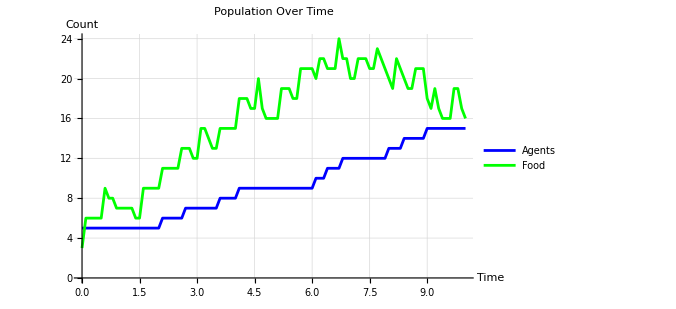

Part::partd: Part specification simulationGraphics[[101]]
     is longer than depth of object.

Part::partd: Part specification simulationGraphics⟦101⟧ is longer than depth of object.

Part::partd: Part specification simulationGraphics[[101]]
     is longer than depth of object.

```mathematica
model = initializeModel[parameters];
Simulation = genSimulationStates[parameters, model, 100];
simulationGraphics = renderSimulation[Simulation, parameters];

Manipulate[simulationGraphics[[j]], {j, 1, Length@simulationGraphics, 1, Appearance->Labeled}]

plotPopulationStats[Simulation]
```

```mathematica
|
```

## Experimentation

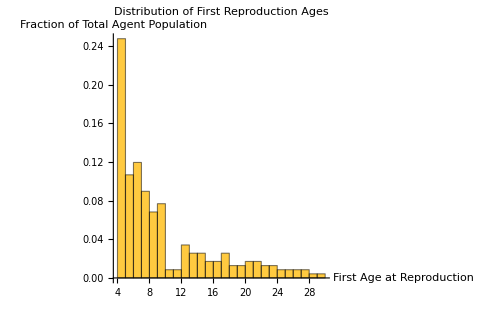
Mean Age at First Reproduction: 9.70
Median Age at First Reproduction: 7.40
How Many Agents Reproduced: 234
Number of Timesteps: 2000
-Graphics-

The distribution of first reproduction ages shows that most agents reproduce almost immediately after reaching the minimum reproduction age, which, in this experiment, was set to 4. Moreover, this suggests that the environment is rich in resources and thus conducive to the population’s growth, as agents can have sufficient energy and food to reproduce immediately and find mates. Additionally, the median first reproduction age of 7.40 furthers this pattern, indicating that at least half of the agents reproduce early in their lifespans. Also, the distribution is right-skewed, which explains the disparity between the mean and median age at first reproduction (9.70 and 7.40, respectively). This gap shows that the population does not behave uniformly, and its reproductive strategies emerge from interactions within the environment.

## Conclusion

## Future Direction

## Acknowledgements

## References